# Evaluation

BX Pan
2017.9.18

There was some variability depending on the geo-graphical area. For instance, over Europe, the anomaly correlations decreased much quicker than over the Northern Hemisphere extratropics as a whole.

Miyakoda et al. (1986) used a 10-day running mean for both the forecasts and the observed data in an attempt to obtain positive skills by filtering out the unpredictable components, most especially the baroclinic eddies

## Cutting

```mathematica
S2SCut[polygon_,s2sdirectory_]:=Block[
{cpcprecip,cpclat,cpclon,cpctime,s2sprecip,s2slat,s2slon,s2stime,
 year=StringTake[StringCases[s2sdirectory,"_"~~__~~"-"],{2,5}][[1]],
 interval,
 points,indexes,cpcdirectory},
    cpcdirectory="/Users/lambda/Documents/Data/CPC_Precipitation/global/precip."<>year<>".nc";
	{cpcprecip,cpclat,cpclon,cpctime}=Map[Import[cpcdirectory,{"Datasets",#}]&,{"precip","lat","lon","time"}];
	{s2sprecip,s2slat,s2slon,s2stime}=Map[Import[s2sdirectory,{"Datasets",#}]&,{"tp","latitude","longitude","time"}];
	interval=Map[Position[Abs[cpctime-#[s2stime]],Min[Abs[cpctime-#[s2stime]]]][[1,1]]&,{Min,Max}];	
    cpcprecip=Block[{DownScale,size},
        DownScale[data_,ratio_]:=Block[{convoluter},
			(* This Function performs spacial average downscaling of 2D data through uniform convolution ratio is kind like {5,4}*) 
			convoluter = Block[{net},
   			net = NetInitialize[ConvolutionLayer[1, ratio, "Stride" -> ratio, 
   						"Input" -> Flatten[{1, Dimensions[data]}]]];
               NetReplacePart[net, {"Weights" -> ConstantArray[1./(ratio/.List->Times), Flatten[{1, 1, ratio}]]}]];
            (convoluter@{data})[[1]]];
        size={Round[Abs[s2slat[[2]]-s2slat[[1]]]/Abs[cpclat[[2]]-cpclat[[1]]]],
          Round[Abs[s2slon[[2]]-s2slon[[1]]]/Abs[cpclon[[2]]-cpclon[[1]]]]};
        Map[DownScale[#,size]&,cpcprecip[[interval[[1]];;interval[[2]]]]]];
    points=Block[{InOrOut,grids},
        InOrOut[point_]:=Block[{singletest},
			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
			(Map[singletest,polygon])/.List->Or];
        grids=Block[{scope=Map[MinMax,Transpose[Flatten[polygon,1]]],lat,lon},
            lat=Select[s2slat,And[#<=scope[[2,2]], #>=scope[[2,1]]]&];
            lon=Select[s2slon,And[#<=scope[[1,2]], #>=scope[[1,1]]]&];
        Table[Table[{lat[[i]],lon[[j]]},{j,Length[lon]}],{i,Length[lat]}]];
        Select[Flatten[grids,1],InOrOut[Reverse[#]]&]];
    indexes=Block[{grids=Table[Table[{s2slat[[i]],s2slon[[j]]},{j,Length[s2slon]}],{i,Length[s2slat]}]},
        Map[Position[grids,#][[1]]&,points]];
    cpcprecip=Map[cpcprecip[[;;,#[[1]],#[[2]]]]&,indexes];
    s2sprecip=Block[{scale,offset,origion},
        {scale,offset}=Import[s2sdirectory,"Annotations"][[6,1;;2,2]];
        origin=Map[(s2sprecip[[;;,;;,#[[1]],#[[2]]]]*scale+offset)&,indexes];
        Transpose[Table[If[i==1,origin[[;;,1,;;]],origin[[;;,i,;;]]-origin[[;;,i-1,;;]]],{i,Dimensions[origin][[2]]}]]];
    {cpcprecip,s2sprecip}]
```

#### Example

```mathematica
polygon=westconus[[1]];
s2sdirectory="/Users/lambda/Documents/Data/S2S/CMA/CMA_1994-01-01.nc";
s2sdirectory="/Users/lambda/Documents/Data/S2S/BoM/Bom_1981-01-01.nc";
s2sdirectory="/Users/lambda/Documents/Data/S2S/ECCC/ECCC_1995-01-05.nc";
s2sdirectory="/Users/lambda/Documents/Data/S2S/ECMWF/ECMWF_1997-01-02.nc";
```

```mathematica
{cpcprecip,s2sprecip}=S2SCut[polygon,s2sdirectory];
```

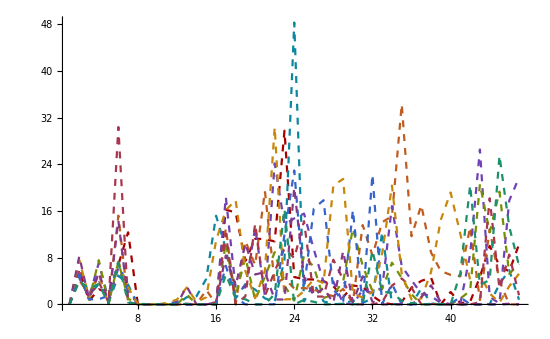
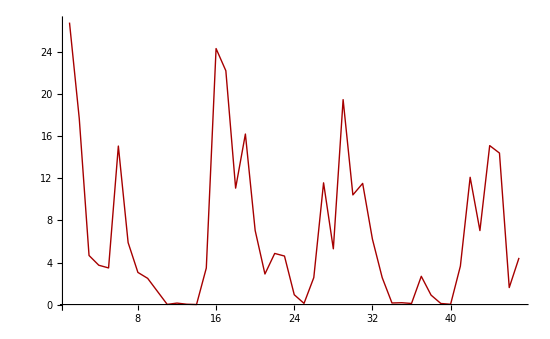

```mathematica
grid=2;
{ListLinePlot[Table[s2sprecip[[grid,;;,i]],{i,Dimensions[s2sprecip][[3]]}],
	PlotStyle->Dashed,
	PlotRange->Full,ImageSize->550],
 ListLinePlot[cpcprecip[[grid,;;]],
    PlotStyle->Thick,PlotRange->Full,ImageSize->550]}
```

## Evaluation

Deterministic Scores

Time Scale

Daily

Weekly

Spatial Scale

Grid

Area Average

Correlation Coefficient(r^2) and Root Mean Square Error(RMSE) are probably not the most suitable for assessing probabilistic forecasts after 10 days, but they are the most widely used for evaluating medium-range weather forecasting and they were used in previous papers on monthly forecasting. It should be Beat Climatology and Persistence (Molteni et al., 1986).

Example: BoM Dataset

#### Sample Collection

The Oct to Feb hindcasts for the West Coast CONUS were gathered as follows. Together there are 161 boreal winter months(33 years).

```mathematica
dataset=Block[{},
	SetDirectory["/Users/lambda/Documents/Data/S2S/BoM"];
	Map["/Users/lambda/Documents/Data/S2S/BoM/"<>#&,
		Flatten[Table[FileNames["*-"<>month<>"-*.nc"],{month,{"01","02","10","11","12"}}]]]];
BoM=Map[S2SCut[polygon,#]&,dataset];
Export["/Users/lambda/Documents/Data/S2S/BoM/BoM_WestCONUS.mx",BoM];
```

#### ReArrange

```mathematica
Dimensions[BoM]
Dimensions[BoM[[1,1]]]
```

{161,2,13}

{13,62}

```mathematica
s2sdirectory=dataset[[-1]];
{cpcprecip,s2sprecip}=S2SCut[polygon,s2sdirectory];
```

```mathematica
dataset[[-1]]
```

/Users/lambda/Documents/Data/S2S/BoM/BoM_2013-12-01.nc

```mathematica
year=ToString[2013];
cpcdirectory="/Users/lambda/Documents/Data/CPC_Precipitation/global/precip."<>year<>".nc";
{cpcprecip,cpclat,cpclon,cpctime}=Map[Import[cpcdirectory,{"Datasets",#}]&,{"precip","lat","lon","time"}];
{s2sprecip,s2slat,s2slon,s2stime}=Map[Import[s2sdirectory,{"Datasets",#}]&,{"tp","latitude","longitude","time"}];
interval=Map[Position[Abs[cpctime-#[s2stime]],Min[Abs[cpctime-#[s2stime]]]][[1,1]]&,{Min,Max}];
```

```mathematica
Table[Dimensions[BoM[[k,1]]],{k,161}]
```

{{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,62},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,60},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30},{13,30}}

```mathematica
Dimensions[BoM[[;;,2]]]
```

{161,13,62,32}

```mathematica
observation[grid_,day_]:=BoM[[;;,1,grid,day]];
simulation[grid_,day_]:=BoM[[;;,2,grid,day,;;]];
```

```mathematica
ListPlot[Table[Correlation[observation[1,32],simulation[1,32][[;;,ensemble]]],{ensemble,32}]]
```

```mathematica
Dimensions[observation[1,3]]
Dimensions[simulation[1,3]]
```

{161}

{161,32}

Probabilistic Scores

#### Relative Operating Characteristics (ROC) Scores

The relative operating characteristics (ROC) scores are based on contingency tables giving the number of observed occurrences and nonoccurrences of an event as a function of the forecast occurrences and nonoccurrences of that event. The events are defined as binary, for instance, the probability that 2-m temperature is in the upper tercile. (Stanski et al. 1989; Mason and Graham 1999; Kharin and Zwiers 2003)

## History of Attempts

```mathematica
Tuples[{1, 2}, 2]
```

{{1,1},{1,2},{2,1},{2,2}}

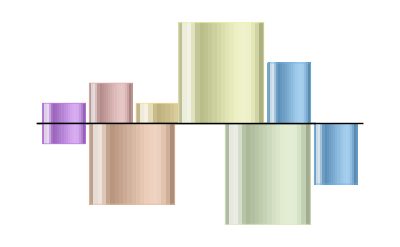

```mathematica
Rotate[Show[{RectangleChart[{{1,1},{1,2},{2,1},{2,-5},{1,-3}},
ChartElementFunction -> "GlassRectangle", ChartStyle -> "Pastel"],
	  RectangleChart[{{1,-1},{2,-4},{2,5},{1,3}}, 
	  ChartElementFunction -> "GlassRectangle", 
	  ChartStyle -> "Pastel"]},Axes->False],Pi/2]
```

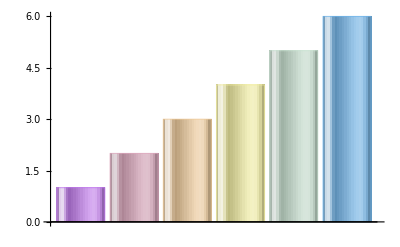

```mathematica
BarChart[Range[6], ChartElementFunction -> "GlassRectangle", 
ChartStyle -> "Pastel"]
```

-Graphics-